## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBA2";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBA2_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/MASSef/examples/FBA2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{{{fdp,Null}},Keq substrate}

{0.00016,Keq value}

{fdp,Km or S05 substrate}

{0.00017,Km or S05 value}

{{{fdp,Null}},kcat substrates}

{10.5,kcat value}

{dhap,Inhibition or activation constant substrate}

{0.00013,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.00003,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.00023,Inhibition or activation constant value}

{{{fdp,Null}},kcat substrates}

{8.17,kcat value}

{fdp,Km or S05 substrate}

{0.00019,Km or S05 value}

{dhap,Inhibition or activation constant substrate}

{9.×10^-6,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.000118,Inhibition or activation constant value}

{g3p,Inhibition or activation constant substrate}

{0.000221,Inhibition or activation constant value}

{{{fdp,Null}},kcat substrates}

{10.33,kcat value}

{fdp,Km or S05 substrate}

{0.00024,Km or S05 value}

{fdp,Km or S05 substrate}

{0.00085,Km or S05 value}

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 8.17 | 7.73
8.6 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 10.33 | 10.03
10.63 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0,0,0};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={1,1,1,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
rxn
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->0},{"prod_inhib_g3p",m["dhap","c"]->0}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

prod inhib

Loading flux equation...

Added inhibition reactions:

{((FBA2^c)_^+dhap^c⇌(FBA2^c&dhap^c)_^)^FBA2_Kic_dhap_1_fdp,((FBA2^c)_^+g3p^c⇌(FBA2^c&g3p^c)_^)^FBA2_Kincc_g3p_1_fdp,((FBA2^c&g3p^c)_^+fdp^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_NC_g3p,((FBA2^c&fdp^c)_^+g3p^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_Kincu_g3p_1_fdp}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating other relative rate forward equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00016
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.32288254562470753

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0.00001652183105507079	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.0909090909090909
1	0	0.000026185337566174318	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.13680688860321005
1	0	0.000041500963250925955	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	0.00006577459413697128	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.0001042457064845785	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.38686317984685686
1	0	0.0001652183105507079	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.0002618533756617432	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.6131368201531431
1	0	0.0004150096325092596	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7152527510491987
1	0	0.0006577459413697135	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7992399910868982
1	0	0.0010424570648457849	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.8631931113967899
1	0	0.0016521831055070788	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0.000058979892851289964	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000058979892851289964	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000058979892851289964	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000058979892851289964	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000058979892851289964	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00011795978570257993	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00011795978570257993	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00011795978570257993	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00011795978570257993	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00011795978570257993	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00023591957140515986	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00023591957140515986	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00023591957140515986	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00023591957140515986	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00023591957140515986	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030538502326548228
1	0	0.00005375872022286247	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08902893154671433
1	0	0.00017000000000000007	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22577346360645933
1	0	0.0005375872022286248	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4390019818156094
1	0	0.0017000000000000008	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6259445813586448
1	0	0.000017000000000000007	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.018351621933368745
1	0	0.00005375872022286247	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05463785271065735
1	0	0.00017000000000000007	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14580581586504698
1	0	0.0005375872022286248	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.30868386452535285
1	0	0.0017000000000000008	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.47728800186120685
1	0	0.000017000000000000007	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010205936112226723
1	0	0.00005375872022286247	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030823877288442242
1	0	0.00017000000000000007	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08534699636986248
1	0	0.0005375872022286248	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.19368986013823766
1	0	0.0017000000000000008	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3235887720780135

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel,haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.32288254562470753

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
lowerParamBound=-6;
upperParamBound=9;
numCPUs=2;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.813345284844
best_fit: 0.988933495991
best_fit: 1.06642011758
best_fit: 1.05142960093
best_fit: 0.792992170762
best_fit: 1.03444791086
best_fit: 1.02161844498
best_fit: 1.00909843738
best_fit: 1.05537619346
best_fit: 0.979980285608

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | haldaneRatio_1 | 7.61924×10^-10 | 5.80528×10^-19 | 2.80703×10^-13 | 1.75439×10^-7 | 0.00016 | 0.00016
1 | relRateFor_fdp | 0.0000276259 | 7.63189×10^-10 | 5.78263×10^-6 | 0.00636089 | 0.0909091 | 0.0909033
1 | relRateFor_fdp | 0.0000225035 | 5.06409×10^-10 | 7.08864×10^-6 | 0.0051815 | 0.136807 | 0.1368
1 | relRateFor_fdp | 0.0000153661 | 2.36116×10^-10 | 7.1031×10^-6 | 0.0035381 | 0.20076 | 0.200753
1 | relRateFor_fdp | 5.99252×10^-6 | 3.59103×10^-11 | 3.929×10^-6 | 0.00137982 | 0.284747 | 0.284743
1 | relRateFor_fdp | 5.40459×10^-6 | 2.92096×10^-11 | 4.81436×10^-6 | 0.00124446 | 0.386863 | 0.386868
1 | relRateFor_fdp | 0.0000180321 | 3.25156×10^-10 | 0.0000207606 | 0.00415213 | 0.5 | 0.500021
1 | relRateFor_fdp | 0.0000306599 | 9.40032×10^-10 | 0.0000432872 | 0.00705996 | 0.613137 | 0.61318
1 | relRateFor_fdp | 0.000042058 | 1.76888×10^-9 | 0.00006927 | 0.00968468 | 0.715253 | 0.715322
1 | relRateFor_fdp | 0.0000514328 | 2.64533×10^-9 | 0.0000946583 | 0.0118435 | 0.79924 | 0.799335
1 | relRateFor_fdp | 0.0000585715 | 3.43062×10^-9 | 0.000116423 | 0.0134875 | 0.863193 | 0.86331
1 | relRateFor_fdp | 0.0000636948 | 4.05703×10^-9 | 0.00013334 | 0.0146674 | 0.909091 | 0.909224
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | absRateFor | 1.66669×10^-8 | 2.77785×10^-16 | 4.02957×10^-7 | 3.83769×10^-6 | 10.5 | 10.5
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000226224 | 5.11772×10^-10 | 3.25554×10^-6 | 0.00520886 | 0.0625 | 0.0624967
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000011139 | 1.24078×10^-10 | 4.46567×10^-6 | 0.00256482 | 0.174112 | 0.174108
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000121026 | 1.46473×10^-10 | 0.0000111471 | 0.00278677 | 0.4 | 0.400011
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000407355 | 1.65938×10^-9 | 0.0000636225 | 0.00938012 | 0.678269 | 0.678332
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000604202 | 3.65061×10^-9 | 0.000120985 | 0.0139132 | 0.869565 | 0.869686
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000200015 | 4.00059×10^-10 | 2.19305×10^-6 | 0.0046054 | 0.047619 | 0.0476169
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000112416 | 1.26375×10^-10 | 3.53394×10^-6 | 0.00258845 | 0.136527 | 0.136524
1 | otherRateRelFor_fdp_prod_inhib_dhap | 8.14967×10^-6 | 6.64172×10^-11 | 6.25516×10^-6 | 0.00187655 | 0.333333 | 0.33334
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000356647 | 1.27197×10^-9 | 0.0000503073 | 0.00821245 | 0.612574 | 0.612624
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000574186 | 3.29689×10^-9 | 0.000110183 | 0.013222 | 0.833333 | 0.833444
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000017296 | 2.99152×10^-10 | 1.28467×10^-6 | 0.00398247 | 0.0322581 | 0.0322568
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000113541 | 1.28915×10^-10 | 2.49297×10^-6 | 0.00261434 | 0.0953577 | 0.0953552
1 | otherRateRelFor_fdp_prod_inhib_dhap | 3.20855×10^-6 | 1.02948×10^-11 | 1.847×10^-6 | 0.0007388 | 0.25 | 0.250002
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.000027992 | 7.83554×10^-10 | 0.0000330768 | 0.00644561 | 0.513167 | 0.5132
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0000521079 | 2.71524×10^-9 | 0.0000923001 | 0.011999 | 0.769231 | 0.769323
1 | otherRateRelFor_fdp_prod_inhib_g3p | 5.14187×10^-6 | 2.64389×10^-11 | 3.59326×10^-7 | 0.00118395 | 0.0303497 | 0.0303493
1 | otherRateRelFor_fdp_prod_inhib_g3p | 2.2037×10^-6 | 4.85631×10^-12 | 4.49184×10^-7 | 0.00050742 | 0.0885231 | 0.0885226
1 | otherRateRelFor_fdp_prod_inhib_g3p | 4.67709×10^-6 | 2.18751×10^-11 | 2.42049×10^-6 | 0.00107694 | 0.224756 | 0.224758
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0000154391 | 2.38367×10^-10 | 0.0000155651 | 0.00355506 | 0.437829 | 0.437845
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0000249074 | 6.2038×10^-10 | 0.0000358619 | 0.00573531 | 0.625283 | 0.625319
1 | otherRateRelFor_fdp_prod_inhib_g3p | 6.36623×10^-7 | 4.05289×10^-13 | 2.67016×10^-8 | 0.000146588 | 0.0182154 | 0.0182154
1 | otherRateRelFor_fdp_prod_inhib_g3p | 2.26573×10^-7 | 5.13351×10^-14 | 2.83062×10^-8 | 0.0000521702 | 0.0542573 | 0.0542573
1 | otherRateRelFor_fdp_prod_inhib_g3p | 8.05337×10^-7 | 6.48567×10^-13 | 2.68804×10^-7 | 0.000185436 | 0.144958 | 0.144958
1 | otherRateRelFor_fdp_prod_inhib_g3p | 2.65488×10^-6 | 7.04841×10^-12 | 1.87994×10^-6 | 0.000611312 | 0.307525 | 0.307527
1 | otherRateRelFor_fdp_prod_inhib_g3p | 4.57756×10^-6 | 2.0954×10^-11 | 5.02264×10^-6 | 0.00105403 | 0.476519 | 0.476524
1 | otherRateRelFor_fdp_prod_inhib_g3p | 2.36844×10^-6 | 5.60953×10^-12 | 5.51996×10^-8 | 0.000545356 | 0.0101218 | 0.0101218
1 | otherRateRelFor_fdp_prod_inhib_g3p | 1.1395×10^-6 | 1.29847×10^-12 | 8.02408×10^-8 | 0.00026238 | 0.0305819 | 0.0305819
1 | otherRateRelFor_fdp_prod_inhib_g3p | 2.1151×10^-6 | 4.47365×10^-12 | 4.12829×10^-7 | 0.000487019 | 0.0847666 | 0.0847662
1 | otherRateRelFor_fdp_prod_inhib_g3p | 8.60275×10^-6 | 7.40073×10^-11 | 3.81863×10^-6 | 0.00198084 | 0.192778 | 0.192775
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0000164172 | 2.69526×10^-10 | 0.0000122054 | 0.00378014 | 0.322883 | 0.32287

### Simulated Data and Best Fit Data Plot

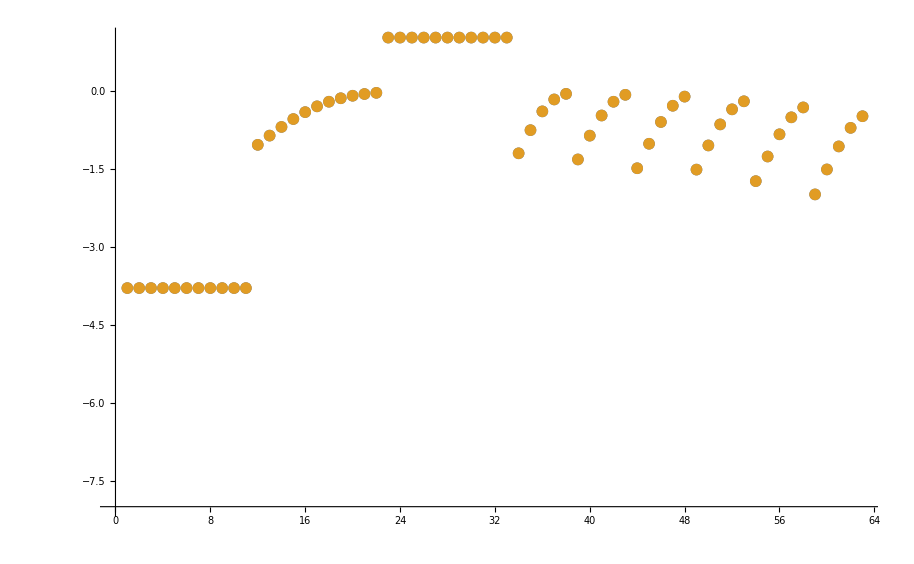

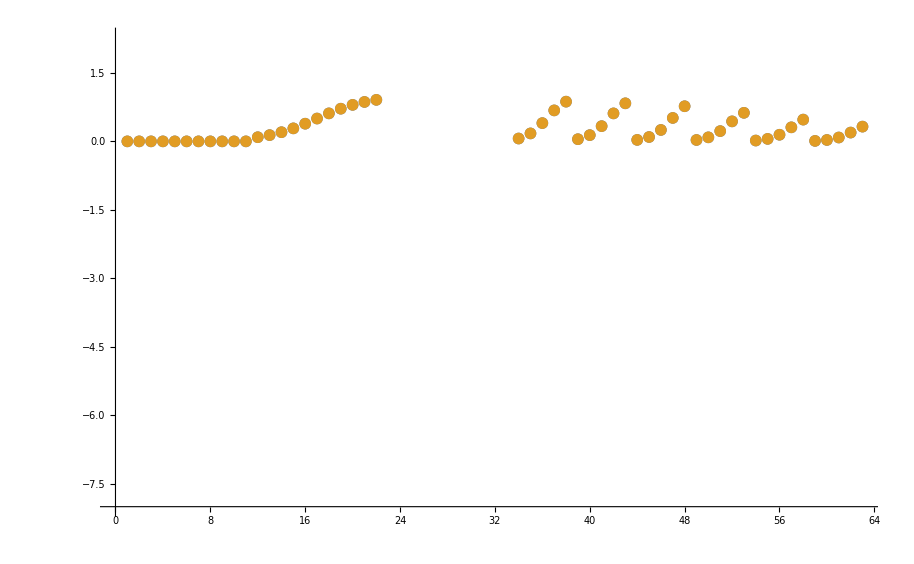

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

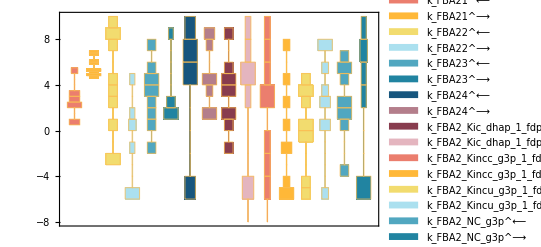

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

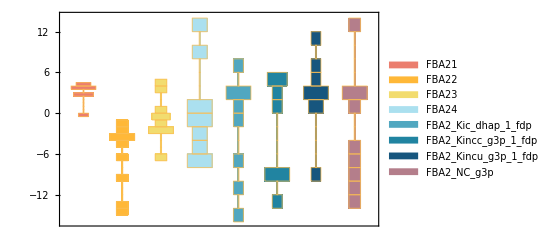

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

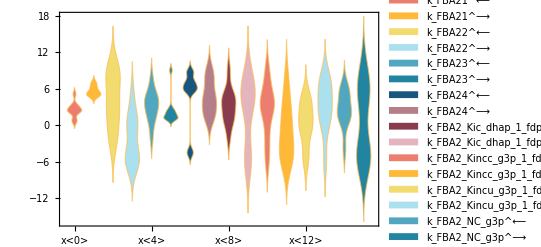

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

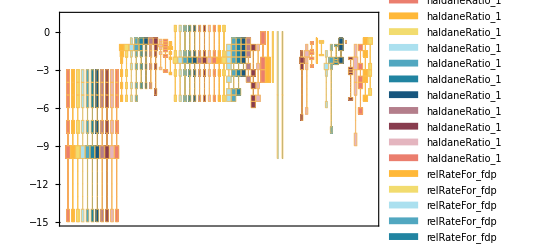

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00017 | 0.000169986 | 0.0083025

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
10.5 | 10.3262 | 1.65528

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.00016 | 1.75439×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.00016 | 1.75439×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
0.00013 | 0.000130008 | 0.00602305
0.00003 | 0.0000300031 | 0.0104657

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %
0.00023 | 0.000229901 | 0.0429731

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

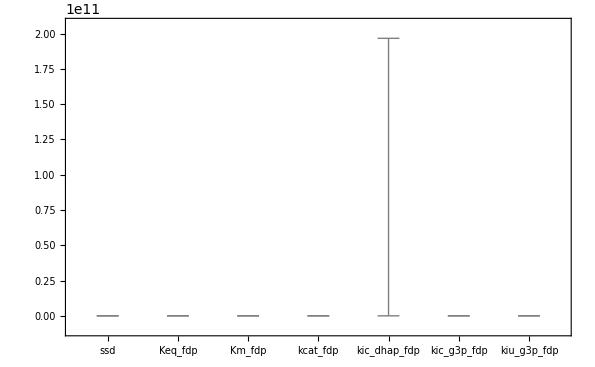

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```